```mathematica
NDSolve[{.01 y''[x]-y'[x]+.01 x^2y[x]==2x,y[0]==2,y[1]==2.01},y[x],{x,0,1}]
```

{{y[x]→InterpolatingFunction[{{0., 1.}}, <>][x]}}

```mathematica
%5⟦1,1,2⟧
```

InterpolatingFunction[{{0., 1.}}, <>][x]

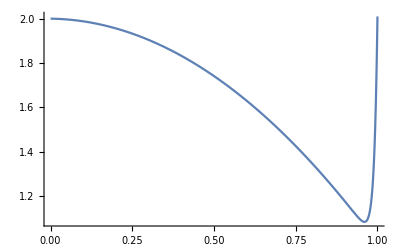

```mathematica
Plot[%6,{x,0.,1.}]
```

```mathematica
Plot[Evaluate[y[x]/.a],{x,0,1}]
```

ReplaceAll::reps: {a} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Expand[-(1+ϵ ξ)^5/5+2/3(1+ϵ ξ)^3-2(1+ϵ ξ)]
```

-23/15-ϵ ξ-(4 ϵ^3 ξ^3)/3-ϵ^4 ξ^4-(ϵ^5 ξ^5)/5

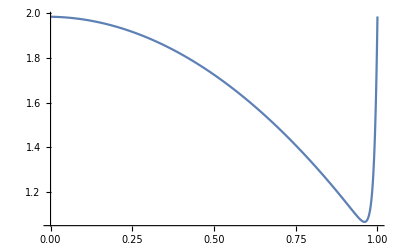

```mathematica
Plot[2-x^2+.01(-23/15-2x+2/3x^3-x^5/5)+Exp[(x-1)/.01]+68/15*.01Exp[(x-1)/.01-1],{x,0,1}]
```

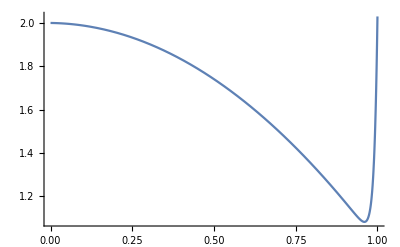

```mathematica
Plot[2-x^2+Exp[(x-1)/.01]+.01(-x^5/5+2x^3/3-2x+68/15Exp[(x-1)/.01]),{x,0,1}]
```

```mathematica
NDSolve
```